Probability that A wins

```mathematica
NSum[Exp[-2] 2^j/(j!)Exp[-3/2](3/2)^k/(k!),{k,0,Infinity},{j,k+1,Infinity}]
```

Probability of a tie as a function of t

```mathematica
tie[t_]:=Exp[-7/2(1-t/90)] NSum[((2-(2t)/90)^k(3/2-t/60)^k)/(k!)^2,{k,0,10}]
```

```mathematica
tie[0]
```

0.216183

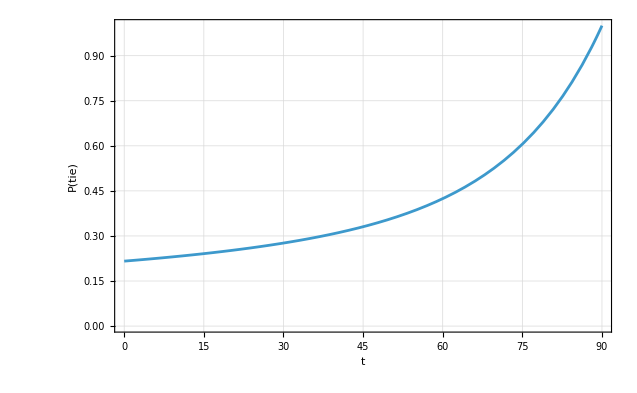

```mathematica
Plot[tie[t],{t,0,90},Frame->True,GridLines->Automatic,LabelStyle->Large,PlotRange->{{0,90},{0,1}},FrameLabel->{"t","P(tie)"}]
```

```mathematica
tie2[t_]:=If[t<60,Exp[-7/2(1-t/90)] NSum[((2-(2t)/90)^k(3/2-t/60)^k)/(k!)^2,{k,0,10}],Exp[-7/2(1-t/90)] NSum[((2-(2t)/90)^k(3/2-t/60)^(k+1))/((k!)(k+1)!),{k,0,10}]]
```

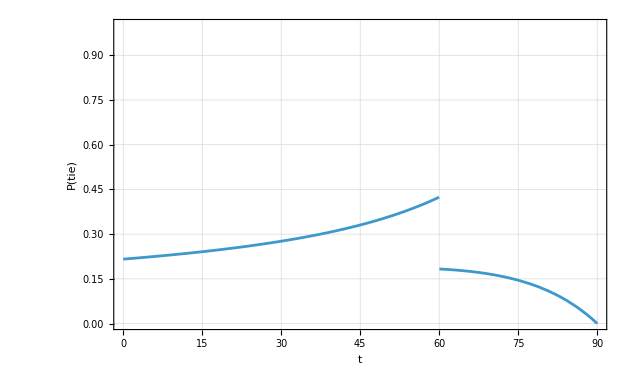

```mathematica
Plot[tie2[t],{t,0,90},Frame->True,GridLines->Automatic,LabelStyle->Large,PlotRange->{{0,90},{0,1}},FrameLabel->{"t","P(tie)"}]
```